```mathematica
Get["E:\\FAKS\\3. LETNIK\\NRO\\2.DN\\MonteCarloPi.m"]

nTock=10000; (*Število naključnih točk*)

priblizekPi=MonteCarloPi[nTock];

Print["Približna vrednost π: ",N[priblizekPi]]
```

Približna vrednost π: 3.132

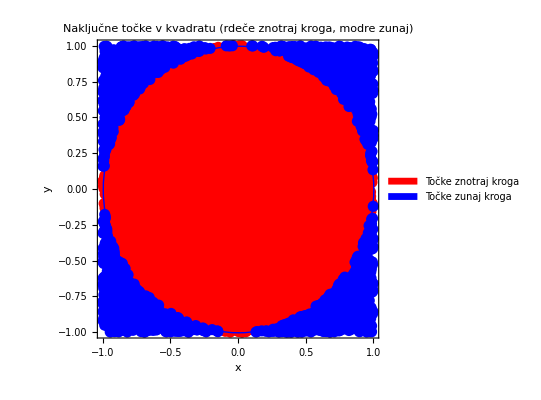

```mathematica
tocke=RandomReal[{-1,1},{nTock,2}]; (*Generiranje naključnih točk v kvadratu*)

vKrog=Select[tocke,Norm[#]<=1&]; (*Izbor točk,ki padejo v krog*)
mimokrog=Select[tocke,Norm[#]>1&]; (*Izbor točk zunaj kroga*)

Legended[Graphics[{PointSize[0.02],Red,Point[vKrog],Blue,Point[mimokrog],Circle[{0,0},1]},Frame->True,FrameLabel->{"x","y","Monte Carlo simulacija za π"},PlotLabel->"Naključne točke v kvadratu (rdeče znotraj kroga, modre zunaj)"],Placed[SwatchLegend[{Red,Blue},{"Točke znotraj kroga","Točke zunaj kroga"}],Automatic]]
```